```mathematica
SetDirectory[NotebookDirectory[]];
PacletDirectoryLoad[Directory[]];
Get["Scrabbology`"]
```

## Version 1: 7 Letter Scrabble-gorithm

```mathematica
CloudConnect[]
```

josephb@wolfram.com

### Run Algorithm

```mathematica
RunVersion1Scrabblegorithm[1]
```

Attempt 1

Bingos Found: {CHIPPED}

Tiles Left: 93 AAAAAAAAABBCDDDEEEEEEEEEEEFFGGGHIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOQRRRRRRSSSSTTTTTTUUUUVVWWXYYZ??

Bingos Found: {CHIPPED,NULLIFY}

Tiles Left: 86 AAAAAAAAABBCDDDEEEEEEEEEEEFGGGHIIIIIIIJKLLMMNNNNNOOOOOOOOQRRRRRRSSSSTTTTTTUUUVVWWXYZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES}

Tiles Left: 79 AAAAAAAAABBCDDDEEEEEEEEEEFGGGHIIIIIIKLLMMNNNNOOOOOOOOQRRRRRSSSTTTTTTUUVVWWXYZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE}

Tiles Left: 72 AAAAAAABBCDDDEEEEEEEEEFGGGHIIIIIIKLMMNNNNOOOOOOOOQRRRRSSSTTTTTUUVWWXYZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE,COMMUNE}

Tiles Left: 65 AAAAAAABBDDDEEEEEEEEFGGGHIIIIIIKLNNNOOOOOOOQRRRRSSSTTTTTUVWWXYZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE,COMMUNE,ADDRESS}

Tiles Left: 58 AAAAAABBDEEEEEEEFGGGHIIIIIIKLNNNOOOOOOOQRRRSTTTTTUVWWXYZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE,COMMUNE,ADDRESS,FORLESE}

Tiles Left: 51 AAAAAABBDEEEEEGGGHIIIIIIKNNNOOOOOOQRRTTTTTUVWWXYZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE,COMMUNE,ADDRESS,FORLESE,NAVARHO}

Tiles Left: 44 AAAABBDEEEEEGGGIIIIIIKNNOOOOOQRTTTTTUWWXYZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE,COMMUNE,ADDRESS,FORLESE,NAVARHO,BORONIA}

Tiles Left: 37 AAABDEEEEEGGGIIIIIKNOOOQTTTTTUWWXYZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE,COMMUNE,ADDRESS,FORLESE,NAVARHO,BORONIA,BIOGENY}

Tiles Left: 30 AAADEEEEGGIIIIKOOQTTTTTUWWXZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE,COMMUNE,ADDRESS,FORLESE,NAVARHO,BORONIA,BIOGENY,QUIXOTE}

Tiles Left: 23 AAADEEEGGIIIKOTTTTWWZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE,COMMUNE,ADDRESS,FORLESE,NAVARHO,BORONIA,BIOGENY,QUIXOTE,TOGATED}

Tiles Left: 16 AAEEGIIIKTTWWZ??

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE,COMMUNE,ADDRESS,FORLESE,NAVARHO,BORONIA,BIOGENY,QUIXOTE,TOGATED,TWAITES}

Tiles Left: 9 AEGIIKWZ?

Bingos Found: {CHIPPED,NULLIFY,INJURES,LARVATE,COMMUNE,ADDRESS,FORLESE,NAVARHO,BORONIA,BIOGENY,QUIXOTE,TOGATED,TWAITES,GAWKIES}

Tiles Left: 2 IZ

Success!

```mathematica
dataV1=CloudGet[URL["https://www.wolframcloud.com/env/josephb/Scrabble/V.1-WordMaster"]];
```

```mathematica
Dataset[dataV1]
```

### Visualize

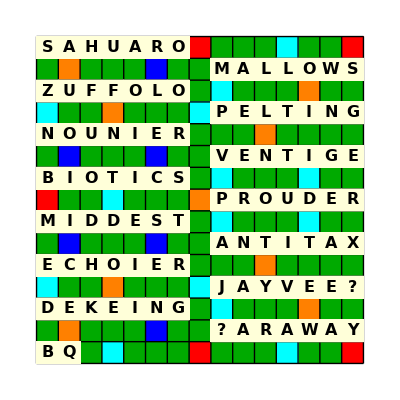

```mathematica
VisualizeVersion1[RandomChoice[dataV1]]
```

## Version 2: 8 Letter Scrabble-gorithm

### Run Algorithm

```mathematica
RunVersion2Scrabblegorithm[1]
```

Bingos: {ALTHAEA}

Tiles Left: 93 AAAAAABBCCDDDDEEEEEEEEEEEFFGGGHIIIIIIIIIJKLLLMMNNNNNNOOOOOOOOPPQRRRRRRSSSSTTTTTUUUUVVWWXYYZ??

Tiles Used: 7 AAAEHLT

OVERKIND played through: E

Bingos: {ALTHAEA,OVERKIND}

Tiles Left: 86 AAAAAABBCCDDDEEEEEEEEEEEFFGGGHIIIIIIIIJLLLMMNNNNNOOOOOOOPPQRRRRRSSSSTTTTTUUUUVWWXYYZ??

Tiles Used: 14 AAADEHIKLNORTV

CHLORIDE played through: R

Bingos: {ALTHAEA,OVERKIND,CHLORIDE}

Tiles Left: 79 AAAAAABBCDDEEEEEEEEEEFFGGGIIIIIIIJLLMMNNNNNOOOOOOPPQRRRRRSSSSTTTTTUUUUVWWXYYZ??

Tiles Used: 21 AAACDDEEHHIIKLLNOORTV

REMERGED played through: D

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED}

Tiles Left: 72 AAAAAABBCDDEEEEEEEFFGGIIIIIIIJLLMNNNNNOOOOOOPPQRRRSSSSTTTTTUUUUVWWXYYZ??

Tiles Used: 28 AAACDDEEEEEGHHIIKLLMNOORRRTV

NITROXYL played through: L

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED,NITROXYL}

Tiles Left: 65 AAAAAABBCDDEEEEEEEFFGGIIIIIIJLLMNNNNOOOOOPPQRRSSSSTTTTUUUUVWWYZ??

Tiles Used: 35 AAACDDEEEEEGHHIIIKLLMNNOOORRRRTTVXY

LUNINESS played through: L

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED,NITROXYL,LUNINESS}

Tiles Left: 58 AAAAAABBCDDEEEEEEFFGGIIIIIJLLMNNOOOOOPPQRRSSTTTTUUUVWWYZ??

Tiles Used: 42 AAACDDEEEEEEGHHIIIIKLLMNNNNOOORRRRSSTTUVXY

QUININAS played through: N

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED,NITROXYL,LUNINESS,QUININAS}

Tiles Left: 51 AAAAABBCDDEEEEEEFFGGIIIJLLMNOOOOOPPRRSTTTTUUVWWYZ??

Tiles Used: 49 AAAACDDEEEEEEGHHIIIIIIKLLMNNNNNOOOQRRRRSSSTTUUVXY

DANEWORT played through: T

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED,NITROXYL,LUNINESS,QUININAS,DANEWORT}

Tiles Left: 44 AAAABBCDEEEEEFFGGIIIJLLMOOOOPPRSTTTTUUVWYZ??

Tiles Used: 56 AAAAACDDDEEEEEEEGHHIIIIIIKLLMNNNNNNOOOOQRRRRRSSSTTUUVWXY

JAMBARTS played through: A

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED,NITROXYL,LUNINESS,QUININAS,DANEWORT,JAMBARTS}

Tiles Left: 37 AAABCDEEEEEFFGGIIILLOOOOPPTTTUUVWYZ??

Tiles Used: 63 AAAAAABCDDDEEEEEEEGHHIIIIIIJKLLMMNNNNNNOOOOQRRRRRRSSSSTTTUUVWXY

UPFILLED played through: I

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED,NITROXYL,LUNINESS,QUININAS,DANEWORT,JAMBARTS,UPFILLED}

Tiles Left: 30 AAABCEEEEFGGIIIOOOOPTTTUVWYZ??

Tiles Used: 70 AAAAAABCDDDDEEEEEEEEFGHHIIIIIIJKLLLLMMNNNNNNOOOOPQRRRRRRSSSSTTTUUUVWXY

PUTATIVE played through: T

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED,NITROXYL,LUNINESS,QUININAS,DANEWORT,JAMBARTS,UPFILLED,PUTATIVE}

Tiles Left: 23 AABCEEEFGGIIOOOOTTWYZ??

Tiles Used: 77 AAAAAAABCDDDDEEEEEEEEEFGHHIIIIIIIJKLLLLMMNNNNNNOOOOPPQRRRRRRSSSSTTTTUUUUVVWXY

FOOTNOTE played through: N

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED,NITROXYL,LUNINESS,QUININAS,DANEWORT,JAMBARTS,UPFILLED,PUTATIVE,FOOTNOTE}

Tiles Left: 16 AABCEEGGIIOWYZ??

Tiles Used: 84 AAAAAAABCDDDDEEEEEEEEEEFFGHHIIIIIIIJKLLLLMMNNNNNNOOOOOOOPPQRRRRRRSSSSTTTTTTUUUUVVWXY

CAPOEIRA played through: P with a blank R

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED,NITROXYL,LUNINESS,QUININAS,DANEWORT,JAMBARTS,UPFILLED,PUTATIVE,FOOTNOTE,CAPOEIRA}

Tiles Left: 9 BEGGIWYZ?

Tiles Used: 91 AAAAAAAAABCCDDDDEEEEEEEEEEEFFGHHIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRRSSSSTTTTTTUUUUVVWXY?

BEWIGGED played through: E with a blank D

Bingos: {ALTHAEA,OVERKIND,CHLORIDE,REMERGED,NITROXYL,LUNINESS,QUININAS,DANEWORT,JAMBARTS,UPFILLED,PUTATIVE,FOOTNOTE,CAPOEIRA,BEWIGGED}

Tiles Left: 2 YZ

Tiles Used: 98 AAAAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRRSSSSTTTTTTUUUUVVWWXY??

Success!

```mathematica
dataV2=CloudGet[URL["https://www.wolframcloud.com/env/josephb/Scrabble/V.2-WordMaster"]];
```

```mathematica
Dataset[dataV2]
```

```mathematica
RandomChoice[dataV2]
```

<|Bingos→{WHEELER,DARRAINS,TOOTHIER,ELLIPTIC,GOPURAMS,TYPESETS,JOINTURE,MORCEAUX,EBONIZED,IDEOLOGY,REVIVIFY,DEARNING,OUABAINS,AQUAFARM},Overlaps→{R,R,I,R,P,U,M,I,E,Y,E,O,A},Blanks→{S,R},Tiles Remaining→{K,W}|>

## Version 3: Actual Scrabble Game

```mathematica
RunScrabblegorithm[]
```

Tiles Used: 7 ACILOST

Tiles Left: 93 AAAAAAAABBCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIIJKLLLMMNNNNNNOOOOOOOPPQRRRRRRSSSTTTTTUUUUVVWWXYYZ??